```mathematica
-Graphics-;
```

```mathematica
solu=LinearSolve[({{1/R1+1/R2+s*C1, -1/R2-s*C1}, {-1/R2, 1/R2+s*C2}}),({{Vin/R1}, {0}})]
```

{{((1+C2 R2 s) Vin)/(1+C2 R1 s+C2 R2 s+C1 C2 R1 R2 s^2)},{Vin/(1+C2 R1 s+C2 R2 s+C1 C2 R1 R2 s^2)}}

```mathematica
Vout=Extract[solu,{2,1}]
```

Vin/(1+C2 R1 s+C2 R2 s+C1 C2 R1 R2 s^2)

```mathematica
H[s]=Vout/Vin
```

1/(1+C2 R1 s+C2 R2 s+C1 C2 R1 R2 s^2)

```mathematica
Hm[s]=TransferFunctionModel[H[s],s]
```

1/(1+C2 R1 s+C2 R2 s+C1 C2 R1 R2 s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[Hm[s]]
```

{{{(-C2 R1-C2 R2-√(-4 C1 C2 R1 R2+(C2 R1+C2 R2)^2))/(2 C1 C2 R1 R2),(-C2 R1-C2 R2+√(-4 C1 C2 R1 R2+(C2 R1+C2 R2)^2))/(2 C1 C2 R1 R2)}}}

```mathematica
Hs[s]=Hm[s]/.{C2->C1,R2-> 1/2 R1}
```

1/(1+(3 C1 R1 s)/2+1/2 C1^2 R1^2 s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
planta[s]=Hs[s]/.{C1->10*10^-9,R1->1/(2*Pi*1000*10*10^-9)}
```

1/(1+(3 s)/(4000 π)+s^2/(8000000 π^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
pplanta=TransferFunctionPoles[planta[s]]
```

{{{-4000 π,-2000 π}}}

```mathematica
p1=Extract[pplanta,{1,1,2}]
```

-2000 π

```mathematica
p2=Extract[pplanta,{1,1,1}]
```

-4000 π

```mathematica
ganancia[s]=TransferFunctionModel[k]
```

kTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11$CellContext`k11FalseFalseFalseAutomaticNoneAutomatic

```mathematica
int[s]=TransferFunctionModel[R3i/(R1i*R2i*C1i*s),s]
```

R3i/(C1i R1i R2i s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`R3i$CellContext`C1i1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
int[s]=Cancel[int[s]/.{R3i->100*10^3,R2i->100*10^3,R1i->100*10^3,C1i-> 1*10^-9}]
```

10000/sTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11100000101FalseFalseFalseAutomaticNoneAutomatic

```mathematica
comp[s]=TransferFunctionModel[(s-(p1-p1*Tan[22.5*Pi/180]))/(s-(p1+p1*Tan[67.5*Pi/180])),s]
```

(3680.6+s)/(21452.1+s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s113680.604738042439721452.1364906759041FalseFalseFalseAutomaticNoneAutomatic

```mathematica
sys[s]=SystemsModelSeriesConnect[SystemsModelSeriesConnect[planta[s],comp[s]],int[s]]
```

(10000 (114122.+31.0063 s))/(s (665151.+189.799 s+0.0158264 s^2+3.92699×10^-7 s^3))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11100000101FalseFalseFalseAutomaticNoneNoneAutomatic

```mathematica
TransferFunctionPoles[sys[s]]
```

{{{-21452.1,-12566.4,-6283.19,0}}}

```mathematica
SystemsModelFeedbackConnect[sys[s]]
```

(5.02408×10^35 (3680.6+1. s))/(5.02408×10^35 (3680.6+1. s)+s (1.07777×10^36+3.0754×10^32 s+2.56442×10^28 s^2+6.36307×10^23 s^3))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s115.02407626824553e355.02407626824553e351FalseFalseFalseAutomaticNoneNoneAutomatic

```mathematica
SystemsModelFeedbackConnect[SystemsModelSeriesConnect[sys[s],ganancia[s]]]
```

(1.2795×10^40 k+3.47634×10^36 k s)/(1.2795×10^40 k+7.45748×10^36 s+3.47634×10^36 k s+2.12798×10^33 s^2+1.77442×10^29 s^3+4.40283×10^24 s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111.279501833017914e407.45748318972408e361FalseFalseFalseAutomaticNoneNoneAutomatic

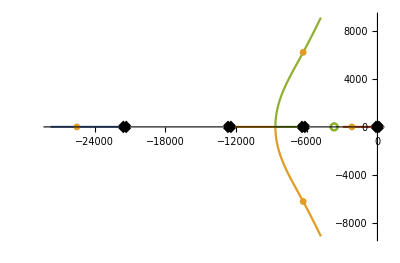

```mathematica
RootLocusPlot[SystemsModelFeedbackConnect[SystemsModelSeriesConnect[sys[s],ganancia[s]]],{k,0,1.5}]
```

```mathematica
(1.279501833017914*^40 k+3.47633588522311*^36 k s)/(1.279501833017914*^40 k+7.45748318972408*^36 s+3.47633588522311*^36 k s+2.127976557526264*^33 s^2+1.7744153396910973*^29 s^3+4.4028308328642453*^24 s^4)/.s->(p1-ⅈ*p1)
```

-((9.04744×10^39-2.18425×10^40 ⅈ) k)/((1.3724×10^40-3.31327×10^40 ⅈ)-(9.04744×10^39-2.18425×10^40 ⅈ) k)

```mathematica
ec=Solve[Abs[-((9.047444226675848*^39-2.184246255685499*^40 ⅈ) k)/((1.3724023980985157*^40-3.313272482522789*^40 ⅈ)-(9.047444226675848*^39-2.184246255685499*^40 ⅈ) k)]==1,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→0.758448+1.1351 ⅈ},{k→0.758448-0.506778 ⅈ}}

```mathematica
Abs[0.758447559174814+1.135096987740603 ⅈ]
```

1.36517

```mathematica
Abs[0.7584475591748151-0.506778457022644 ⅈ]
```

0.912177